```mathematica
Clear[MyRegionPlot]
```

```mathematica
MyRegionPlot[parRangeX_,parRangeY_,domEigs_,Feas_,colour_,background_:False]:=
Which[
background==True,
RegionPlot[
parRangeX[[1]]>0,
parRangeX,parRangeY,
PlotStyle->Directive[Opacity[0.3],colour],
BoundaryStyle->None]
,
background==False,
RegionPlot[
Evaluate@Thread[
Evaluate[Feas]&&
Evaluate@Thread[domEigs<0]],
parRangeX,parRangeY,
MaxRecursion->10,
PlotPoints-> 50,
BoundaryStyle->None,
PlotStyle->Directive[Opacity[0.3],colour],
PlotLegends->None]
]
```

## Fig2

## Fig2abc

```mathematica
parRangeX={k,0,10};
parRangeY={aPΝ,0,4};
```

### Fig2a

```mathematica
pars = kaPΝparsH;
```

```mathematica
equilP=equil/.pars;
Jeq=J/.equil/.pars/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0/.{ComplexInfinity-> 0, Indeterminate-> 0};

FeasRΝP= R >0 && Ν > 0 && P>0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasRΝ = R >0 && Ν > 0 && P≤ 0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasRP = R >0 && Ν ≤  0 && P>0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasR   = R >0 && Ν ≤  0 && P≤ 0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. k ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

```mathematica
(* 
RegionsStable = RegionPlot[
 Evaluate@Thread[domEigs<0],
parRangeX,parRangeY,
MaxRecursion->1,
PlotLegends->Table[i,{i,Dimensions[domEigs][[1]]}]]
*)
```

```mathematica
(*
RegionsUnstable = RegionPlot[
Evaluate[Apply[Or,Thread[domEigs<0]]],
parRangeX,parRangeY,
PlotPoints->20,
MaxRecursion->1]
*)
```

#### SubPlots

```mathematica
RegionsBackground=Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasR,LightGray,True];
```

```mathematica
RegionsR = Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasR,Green]
```

```mathematica
RegionsRΝ = Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRΝ,Blue]
```

```mathematica
RegionsRP =  Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRP,Red]
```

```mathematica
RegionsRΝP =  Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRΝP,Purple]
```

```mathematica
Fig2a =Show[RegionsBackground,RegionsR,RegionsRΝ,RegionsRP,RegionsRΝP]
```

## Fig3

## Fig3abc

```mathematica
parRangeX={c0,0,1};
parRangeY={aPΝ,0,2};
```

### Fig3a

```mathematica
pars=c0aPΝparsH;
```

```mathematica
equilP=equil/.pars;
Jeq=J/.equil/.pars/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0/.{ComplexInfinity-> 0, Indeterminate-> 0};

FeasRΝP= R >0 && Ν > 0 && P>0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasRΝ = R >0 && Ν > 0 && P≤ 0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasRP = R >0 && Ν ≤  0 && P>0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasR   = R >0 && Ν ≤  0 && P≤ 0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
```

```mathematica
(* 
RegionsStable = RegionPlot[
 Evaluate@Thread[domEigs<0],
parRangeX,parRangeY,
MaxRecursion->1,
PlotLegends->Table[i,{i,Dimensions[domEigs][[1]]}]]
*)
```

```mathematica
(*
RegionsUnstable = RegionPlot[
Evaluate[Apply[Or,Thread[domEigs<0]]],
parRangeX,parRangeY,
PlotPoints->20,
MaxRecursion->1]
*)
```

#### SubPlots

```mathematica
RegionsBackground=Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasR,LightGray,True];
```

```mathematica
RegionsR = Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasR,Green]
```

Which[True==True,RegionPlot[a>0,{a,0,100},{b,0,100},PlotStyle→LightGray,BoundaryStyle→None],RegionPlot[Evaluate[Thread[Evaluate[R>0&&Ν≤0&&P≤0&&0≤eΝ≤1&&0≤eP≤1/.equilP$397996]&&Evaluate[Thread[domEigs$397996<0]]]],{k,0,10},{aPΝ,0,4},MaxRecursion→10,PlotPoints→50,BoundaryStyle→None,PlotStyle→Directive[Opacity[0.3],RGBColor[0, 1, 0]],PlotLegends→None]]

```mathematica
RegionsRΝ = Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRΝ,Blue]
```

```mathematica
RegionsRP =  Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRP,Red]
```

```mathematica
RegionsRΝP =  Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRΝP,Purple]
```

```mathematica
Fig3a =Show[RegionsBackground,RegionsR,RegionsRΝ,RegionsRP,RegionsRΝP]
```

## Fig5

## Fig5abc

```mathematica
parRangeX={k,0,10};
parRangeY={aPΝ,0,4};

Get["Figs/temp/equil_suboptN.mx"];
```

### Fig5a

```mathematica
pars=kaPΝparsH;
```

```mathematica
equilP=equil/.pars;
Jeq=J/.equil/.pars/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0/.{ComplexInfinity-> 0, Indeterminate-> 0};

FeasRΝP= R >0 && Ν > 0 && P>0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasRΝ = R >0 && Ν > 0 && P≤ 0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasRP = R >0 && Ν ≤  0 && P>0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasR   = R >0 && Ν ≤  0 && P≤ 0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/k encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/((0.072+0.4 aPΝ) k) encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/k encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1+(1.25 (-1.33631 √(0.+0.0896 k) √k-0.4 k))/k+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

```mathematica
(* 
RegionsStable = RegionPlot[
 Evaluate@Thread[domEigs<0],
parRangeX,parRangeY,
MaxRecursion->1,
PlotLegends->Table[i,{i,Dimensions[domEigs][[1]]}]]
*)
```

```mathematica
(*
RegionsUnstable = RegionPlot[
Evaluate[Apply[Or,Thread[domEigs<0]]],
parRangeX,parRangeY,
PlotPoints->20,
MaxRecursion->1]
*)
```

#### SubPlots

```mathematica
RegionsBackground=Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasR,LightGray,True];
```

```mathematica
RegionsR = Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasR,Green]
```

```mathematica
RegionsRΝ = Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRΝ,Blue]
```

```mathematica
RegionsRP =  Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRP,Red]
```

```mathematica
RegionsRΝP =  Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRΝP,Purple]
```

```mathematica
Fig5a =Show[RegionsBackground,RegionsR,RegionsRΝ,RegionsRP,RegionsRΝP]
```

## Fig5de

```mathematica
parRangeX={k,0,5};
parRangeY={aPΝ,0,4};

Get["Figs/temp/equil_naiveN.mx"];
```

### Fig5d

```mathematica
pars=kaPΝparsM;
```

```mathematica
equilP=equil/.pars;
Jeq=J/.equil/.pars/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0/.{ComplexInfinity-> 0, Indeterminate-> 0};

FeasRΝP= R >0 && Ν > 0 && P>0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasRΝ = R >0 && Ν > 0 && P≤ 0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasRP = R >0 && Ν ≤  0 && P>0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasR   = R >0 && Ν ≤  0 && P≤ 0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/k encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/((0.072+0.4 aPΝ) k) encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/k encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1+(1.25 (-1.33631 √(0.+0.0896 k) √k-0.4 k))/k+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

```mathematica
(* 
RegionsStable = RegionPlot[
 Evaluate@Thread[domEigs<0],
parRangeX,parRangeY,
MaxRecursion->1,
PlotLegends->Table[i,{i,Dimensions[domEigs][[1]]}]]
*)
```

```mathematica
(*
RegionsUnstable = RegionPlot[
Evaluate[Apply[Or,Thread[domEigs<0]]],
parRangeX,parRangeY,
PlotPoints->20,
MaxRecursion->1]
*)
```

#### SubPlots

```mathematica
RegionsBackground=Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasR,LightGray,True];
```

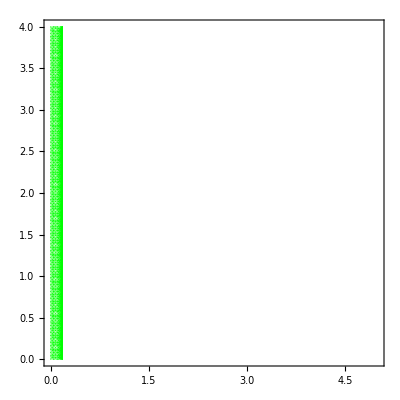

```mathematica
RegionsR = Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasR,Green]
```

```mathematica
RegionsRΝ = Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRΝ,Blue]
```

```mathematica
RegionsRP =  Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRP,Red]
```

```mathematica
RegionsRΝP =  Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRΝP,Purple]
```

```mathematica
Fig5d =Show[RegionsBackground,RegionsR,RegionsRΝ,RegionsRP,RegionsRΝP]
```

### Fig5e

```mathematica
pars=kaPΝparsL;
```

```mathematica
equilP=equil/.pars;
Jeq=J/.equil/.pars/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0/.{ComplexInfinity-> 0, Indeterminate-> 0};

FeasRΝP= R >0 && Ν > 0 && P>0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasRΝ = R >0 && Ν > 0 && P≤ 0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasRP = R >0 && Ν ≤  0 && P>0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
FeasR   = R >0 && Ν ≤  0 && P≤ 0 && 0 ≤ eΝ ≤ 1 && 0 ≤ eP ≤ 1/. equilP;
```

```mathematica
(* 
RegionsStable = RegionPlot[
 Evaluate@Thread[domEigs<0],
parRangeX,parRangeY,
MaxRecursion->1,
PlotLegends->Table[i,{i,Dimensions[domEigs][[1]]}]]
*)
```

```mathematica
(*
RegionsUnstable = RegionPlot[
Evaluate[Apply[Or,Thread[domEigs<0]]],
parRangeX,parRangeY,
PlotPoints->20,
MaxRecursion->1]
*)
```

#### SubPlots

```mathematica
RegionsBackground=Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasR,LightGray,True];
```

```mathematica
RegionsR = Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasR,Green]
```

```mathematica
RegionsRΝ = Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRΝ,Blue]
```

```mathematica
RegionsRP =  Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRP,Red]
```

```mathematica
RegionsRΝP =  Quiet@MyRegionPlot[parRangeX,parRangeY,domEigs,FeasRΝP,Purple]
```

```mathematica
Fig5e =Show[RegionsBackground,RegionsR,RegionsRΝ,RegionsRP,RegionsRΝP]
```